```mathematica
PauliPosN[n_,dim_,l_]:=Nest[ArrayFlatten,Apply[Outer,{Times}~Join~Table[If[currn==n,ℏ/2 PauliMatrix[dim],IdentityMatrix[2]],{currn,l}]],l-1];
HfromJ[J_,size_]:=ω/ℏ Sum[
Sum[
J[[i,j]]*Dot[
PauliPosN[i,dim,size],
PauliPosN[j,dim,size]],
{i,size},{j,size}],
{dim,1,3}]
NormSystem[sys_]:={sys[[1]],Normalize/@sys[[2]]}
Kron[a_,b_]:=ArrayFlatten[Outer[Times,a,b],1]
```

```mathematica
NoSys=2;
NoBath=3;
Jsep=ConstantArray[0,{NoSys+NoBath,NoSys+NoBath}];
BathEigen=Normalize/@Eigenvectors[HfromJ[DiagonalMatrix[ConstantArray[1,NoBath-1],1],NoBath]];
SysEigen=Normalize/@Eigenvectors[HfromJ[DiagonalMatrix[ConstantArray[1,NoSys-1],1],NoSys]];
Jsb=DiagonalMatrix[
ArrayFlatten[{ConstantArray[1,NoSys-1],{b},ConstantArray[1,NoBath-1]},1],
1];
Jsb[[1]][[-1]]=b;(*the last-bath to first system connection*)
(*matrix with the connection from the system states*)
Jsb//MatrixForm
```

(0 | 1 | 0 | 0 | b
0 | 0 | b | 0 | 0
0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0)

```mathematica
SBEigenvec=Normalize/@Eigenvectors[N[HfromJ[Jsb,NoSys+NoBath]/.b->0]];
ConEigenvec=Normalize/@Eigenvectors[N[HfromJ[Jsb,NoSys+NoBath]/.b->1]];
ConEigenval=Eigenvalues[N[HfromJ[Jsb,NoSys+NoBath]/.b->1]];
Chop[Table[Dot[i,j],{i,SBEigenvec},{j,SBEigenvec}]]==IdentityMatrix[2^(NoSys+NoBath)]
Chop[Table[Dot[i,j],{i,ConEigenvec},{j,ConEigenvec}]]==IdentityMatrix[2^(NoSys+NoBath)]
```

True

True

```mathematica
ConEigenvecSYM=Normalize/@Eigenvectors[HfromJ[Jsb,NoSys+NoBath]/.b->1];
Chop[Table[Dot[i,j],{i,ConEigenvecSYM},{j,ConEigenvecSYM}]]==IdentityMatrix[2^(NoSys+NoBath)] (*This evaluates to false as matematica cannot/will not orth symbolic arrays*)
```

False

```mathematica
Phi=Normalize[SBEigenvec[[1]]+SBEigenvec[[2]]];
Phioft=Sum[Phi.v[[1]] ⅇ^(- ⅈ v[[2]] t/ℏ) v[[1]],{v,Transpose[{ConEigenvec,ConEigenval}]}];
rho=Outer[Times,Conjugate[Phioft],Phioft];
```

```mathematica
reduceddensityop=Sum[
ConjugateTranspose[Kron[bathstate,IdentityMatrix[2^NoSys]]].rho.
Kron[bathstate,IdentityMatrix[2^NoSys]],{bathstate,BathEigen}];(*calculate the reduced operator (encodes time dependance) via explicit partial trace and apply it to the eigenstates of energy*)
reduceddensity=Table[S1.reduceddensityop.S2,{S1,SysEigen},{S2,SysEigen}];
Simplify[reduceddensity,ω∈Reals&&t∈Reals]//MatrixForm;
Simplify[Chop[Tr[reduceddensity]],ω∈Reals&&t∈Reals];
```

```mathematica
reduceddensityN=Table[Sum[Kron[S1,b].Conjugate[Phioft] × Phioft.Kron[S2,b],
{b,BathEigen}],
{S1,SysEigen},{S2,SysEigen}];(*implicitly take the partial tracevia sum over bath states*)
Simplify[Chop[Tr[reduceddensityN]],ω∈Reals&&t∈Reals]
Chop[reduceddensityN-reduceddensity/.{t->1,ω->1}]//MatrixForm
```

ⅇ^((0.-1.47214 ⅈ) t ω) ((0.00421605 ⅇ^((0.+1.1041 ⅈ) t ω)-0.0292181 ⅇ^((0.+1.1041 ⅈ) t ω)+0.0034521 ⅇ^((0.+1.1041 ⅈ) t ω)-0.0144526 ⅇ^((0.+3.34017 ⅈ) t ω)-0.372246 ⅇ^((0.+3.34017 ⅈ) t ω)) Conjugate[0.0034521 ⅇ^((0.-0.368034 ⅈ) t ω)-0.0292181 ⅇ^((0.-0.368034 ⅈ) t ω)+0.00421605 ⅇ^((0.-0.368034 ⅈ) t ω)-0.0144526 ⅇ^((0.+1.86803 ⅈ) t ω)-0.372246 ⅇ^((0.+1.86803 ⅈ) t ω)]+(-0.000189213 ⅇ^((0.+1.1041 ⅈ) t ω)+0.0253739 ⅇ^((0.+1.1041 ⅈ) t ω)+0.00968388 ⅇ^((0.+1.1041 ⅈ) t ω)+2.23153×10^-7 ⅇ^((0.+3.34017 ⅈ) t ω)-0.238993 ⅇ^((0.+3.34017 ⅈ) t ω)) Conjugate[0.00968388 ⅇ^((0.-0.368034 ⅈ) t ω)+0.0253739 ⅇ^((0.-0.368034 ⅈ) t ω)-0.000189213 ⅇ^((0.-0.368034 ⅈ) t ω)+2.23153×10^-7 ⅇ^((0.+1.86803 ⅈ) t ω)-0.238993 ⅇ^((0.+1.86803 ⅈ) t ω)]+0.00390989 ⅇ^((0.+1.1041 ⅈ) t ω) Conjugate[0.0191209 ⅇ^((0.-0.368034 ⅈ) t ω)+0.0118377 ⅇ^((0.-0.368034 ⅈ) t ω)+0.00390989 ⅇ^((0.-0.368034 ⅈ) t ω)-0.0144527 ⅇ^((0.+1.86803 ⅈ) t ω)-0.22454 ⅇ^((0.+1.86803 ⅈ) t ω)]+0.0118377 ⅇ^((0.+1.1041 ⅈ) t ω) Conjugate[0.0191209 ⅇ^((0.-0.368034 ⅈ) t ω)+0.0118377 ⅇ^((0.-0.368034 ⅈ) t ω)+0.00390989 ⅇ^((0.-0.368034 ⅈ) t ω)-0.0144527 ⅇ^((0.+1.86803 ⅈ) t ω)-0.22454 ⅇ^((0.+1.86803 ⅈ) t ω)]+0.0191209 ⅇ^((0.+1.1041 ⅈ) t ω) Conjugate[0.0191209 ⅇ^((0.-0.368034 ⅈ) t ω)+0.0118377 ⅇ^((0.-0.368034 ⅈ) t ω)+0.00390989 ⅇ^((0.-0.368034 ⅈ) t ω)-0.0144527 ⅇ^((0.+1.86803 ⅈ) t ω)-0.22454 ⅇ^((0.+1.86803 ⅈ) t ω)]-0.0144527 ⅇ^((0.+3.34017 ⅈ) t ω) Conjugate[0.0191209 ⅇ^((0.-0.368034 ⅈ) t ω)+0.0118377 ⅇ^((0.-0.368034 ⅈ) t ω)+0.00390989 ⅇ^((0.-0.368034 ⅈ) t ω)-0.0144527 ⅇ^((0.+1.86803 ⅈ) t ω)-0.22454 ⅇ^((0.+1.86803 ⅈ) t ω)]-0.22454 ⅇ^((0.+3.34017 ⅈ) t ω) Conjugate[0.0191209 ⅇ^((0.-0.368034 ⅈ) t ω)+0.0118377 ⅇ^((0.-0.368034 ⅈ) t ω)+0.00390989 ⅇ^((0.-0.368034 ⅈ) t ω)-0.0144527 ⅇ^((0.+1.86803 ⅈ) t ω)-0.22454 ⅇ^((0.+1.86803 ⅈ) t ω)]+0.0110378 ⅇ^((0.+1.1041 ⅈ) t ω) Conjugate[0.00903772 ⅇ^((0.-0.368034 ⅈ) t ω)-0.076494 ⅇ^((0.-0.368034 ⅈ) t ω)+0.0110378 ⅇ^((0.-0.368034 ⅈ) t ω)-0.00552041 ⅇ^((0.+1.86803 ⅈ) t ω)-0.142185 ⅇ^((0.+1.86803 ⅈ) t ω)]-0.076494 ⅇ^((0.+1.1041 ⅈ) t ω) Conjugate[0.00903772 ⅇ^((0.-0.368034 ⅈ) t ω)-0.076494 ⅇ^((0.-0.368034 ⅈ) t ω)+0.0110378 ⅇ^((0.-0.368034 ⅈ) t ω)-0.00552041 ⅇ^((0.+1.86803 ⅈ) t ω)-0.142185 ⅇ^((0.+1.86803 ⅈ) t ω)]+0.00903772 ⅇ^((0.+1.1041 ⅈ) t ω) Conjugate[0.00903772 ⅇ^((0.-0.368034 ⅈ) t ω)-0.076494 ⅇ^((0.-0.368034 ⅈ) t ω)+0.0110378 ⅇ^((0.-0.368034 ⅈ) t ω)-0.00552041 ⅇ^((0.+1.86803 ⅈ) t ω)-0.142185 ⅇ^((0.+1.86803 ⅈ) t ω)]-0.00552041 ⅇ^((0.+3.34017 ⅈ) t ω) Conjugate[0.00903772 ⅇ^((0.-0.368034 ⅈ) t ω)-0.076494 ⅇ^((0.-0.368034 ⅈ) t ω)+0.0110378 ⅇ^((0.-0.368034 ⅈ) t ω)-0.00552041 ⅇ^((0.+1.86803 ⅈ) t ω)-0.142185 ⅇ^((0.+1.86803 ⅈ) t ω)]-0.142185 ⅇ^((0.+3.34017 ⅈ) t ω) Conjugate[0.00903772 ⅇ^((0.-0.368034 ⅈ) t ω)-0.076494 ⅇ^((0.-0.368034 ⅈ) t ω)+0.0110378 ⅇ^((0.-0.368034 ⅈ) t ω)-0.00552041 ⅇ^((0.+1.86803 ⅈ) t ω)-0.142185 ⅇ^((0.+1.86803 ⅈ) t ω)]-0.000495365 ⅇ^((0.+1.1041 ⅈ) t ω) Conjugate[0.0253527 ⅇ^((0.-0.368034 ⅈ) t ω)+0.0664297 ⅇ^((0.-0.368034 ⅈ) t ω)-0.000495365 ⅇ^((0.-0.368034 ⅈ) t ω)+8.52367×10^-8 ⅇ^((0.+1.86803 ⅈ) t ω)-0.0912872 ⅇ^((0.+1.86803 ⅈ) t ω)]+0.0664297 ⅇ^((0.+1.1041 ⅈ) t ω) Conjugate[0.0253527 ⅇ^((0.-0.368034 ⅈ) t ω)+0.0664297 ⅇ^((0.-0.368034 ⅈ) t ω)-0.000495365 ⅇ^((0.-0.368034 ⅈ) t ω)+8.52367×10^-8 ⅇ^((0.+1.86803 ⅈ) t ω)-0.0912872 ⅇ^((0.+1.86803 ⅈ) t ω)]+0.0253527 ⅇ^((0.+1.1041 ⅈ) t ω) Conjugate[0.0253527 ⅇ^((0.-0.368034 ⅈ) t ω)+0.0664297 ⅇ^((0.-0.368034 ⅈ) t ω)-0.000495365 ⅇ^((0.-0.368034 ⅈ) t ω)+8.52367×10^-8 ⅇ^((0.+1.86803 ⅈ) t ω)-0.0912872 ⅇ^((0.+1.86803 ⅈ) t ω)]+8.52367×10^-8 ⅇ^((0.+3.34017 ⅈ) t ω) Conjugate[0.0253527 ⅇ^((0.-0.368034 ⅈ) t ω)+0.0664297 ⅇ^((0.-0.368034 ⅈ) t ω)-0.000495365 ⅇ^((0.-0.368034 ⅈ) t ω)+8.52367×10^-8 ⅇ^((0.+1.86803 ⅈ) t ω)-0.0912872 ⅇ^((0.+1.86803 ⅈ) t ω)]-0.0912872 ⅇ^((0.+3.34017 ⅈ) t ω) Conjugate[0.0253527 ⅇ^((0.-0.368034 ⅈ) t ω)+0.0664297 ⅇ^((0.-0.368034 ⅈ) t ω)-0.000495365 ⅇ^((0.-0.368034 ⅈ) t ω)+8.52367×10^-8 ⅇ^((0.+1.86803 ⅈ) t ω)-0.0912872 ⅇ^((0.+1.86803 ⅈ) t ω)]+0.0102362 ⅇ^((0.+1.1041 ⅈ) t ω) Conjugate[0.0500593 ⅇ^((0.-0.368034 ⅈ) t ω)+0.0309916 ⅇ^((0.-0.368034 ⅈ) t ω)+0.0102362 ⅇ^((0.-0.368034 ⅈ) t ω)-0.00552046 ⅇ^((0.+1.86803 ⅈ) t ω)-0.0857666 ⅇ^((0.+1.86803 ⅈ) t ω)]+0.0309916 ⅇ^((0.+1.1041 ⅈ) t ω) Conjugate[0.0500593 ⅇ^((0.-0.368034 ⅈ) t ω)+0.0309916 ⅇ^((0.-0.368034 ⅈ) t ω)+0.0102362 ⅇ^((0.-0.368034 ⅈ) t ω)-0.00552046 ⅇ^((0.+1.86803 ⅈ) t ω)-0.0857666 ⅇ^((0.+1.86803 ⅈ) t ω)]+0.0500593 ⅇ^((0.+1.1041 ⅈ) t ω) Conjugate[0.0500593 ⅇ^((0.-0.368034 ⅈ) t ω)+0.0309916 ⅇ^((0.-0.368034 ⅈ) t ω)+0.0102362 ⅇ^((0.-0.368034 ⅈ) t ω)-0.00552046 ⅇ^((0.+1.86803 ⅈ) t ω)-0.0857666 ⅇ^((0.+1.86803 ⅈ) t ω)]-0.00552046 ⅇ^((0.+3.34017 ⅈ) t ω) Conjugate[0.0500593 ⅇ^((0.-0.368034 ⅈ) t ω)+0.0309916 ⅇ^((0.-0.368034 ⅈ) t ω)+0.0102362 ⅇ^((0.-0.368034 ⅈ) t ω)-0.00552046 ⅇ^((0.+1.86803 ⅈ) t ω)-0.0857666 ⅇ^((0.+1.86803 ⅈ) t ω)]-0.0857666 ⅇ^((0.+3.34017 ⅈ) t ω) Conjugate[0.0500593 ⅇ^((0.-0.368034 ⅈ) t ω)+0.0309916 ⅇ^((0.-0.368034 ⅈ) t ω)+0.0102362 ⅇ^((0.-0.368034 ⅈ) t ω)-0.00552046 ⅇ^((0.+1.86803 ⅈ) t ω)-0.0857666 ⅇ^((0.+1.86803 ⅈ) t ω)]-0.00111535 ⅇ^((0.+1.1041 ⅈ) t ω) Conjugate[0.00287899 ⅇ^((0.-0.368034 ⅈ) t ω)+0.0197863 ⅇ^((0.-0.368034 ⅈ) t ω)-0.00111535 ⅇ^((0.-0.368034 ⅈ) t ω)+0.397958 ⅇ^((0.+1.86803 ⅈ) t ω)-0.0112597 ⅇ^((0.+1.86803 ⅈ) t ω)]+0.0197863 ⅇ^((0.+1.1041 ⅈ) t ω) Conjugate[0.00287899 ⅇ^((0.-0.368034 ⅈ) t ω)+0.0197863 ⅇ^((0.-0.368034 ⅈ) t ω)-0.00111535 ⅇ^((0.-0.368034 ⅈ) t ω)+0.397958 ⅇ^((0.+1.86803 ⅈ) t ω)-0.0112597 ⅇ^((0.+1.86803 ⅈ) t ω)]+0.00287899 ⅇ^((0.+1.1041 ⅈ) t ω) Conjugate[0.00287899 ⅇ^((0.-0.368034 ⅈ) t ω)+0.0197863 ⅇ^((0.-0.368034 ⅈ) t ω)-0.00111535 ⅇ^((0.-0.368034 ⅈ) t ω)+0.397958 ⅇ^((0.+1.86803 ⅈ) t ω)-0.0112597 ⅇ^((0.+1.86803 ⅈ) t ω)]+0.397958 ⅇ^((0.+3.34017 ⅈ) t ω) Conjugate[0.00287899 ⅇ^((0.-0.368034 ⅈ) t ω)+0.0197863 ⅇ^((0.-0.368034 ⅈ) t ω)-0.00111535 ⅇ^((0.-0.368034 ⅈ) t ω)+0.397958 ⅇ^((0.+1.86803 ⅈ) t ω)-0.0112597 ⅇ^((0.+1.86803 ⅈ) t ω)]-0.0112597 ⅇ^((0.+3.34017 ⅈ) t ω) Conjugate[0.00287899 ⅇ^((0.-0.368034 ⅈ) t ω)+0.0197863 ⅇ^((0.-0.368034 ⅈ) t ω)-0.00111535 ⅇ^((0.-0.368034 ⅈ) t ω)+0.397958 ⅇ^((0.+1.86803 ⅈ) t ω)-0.0112597 ⅇ^((0.+1.86803 ⅈ) t ω)]+0.00663249 ⅇ^((0.+1.1041 ⅈ) t ω) Conjugate[0.0152695 ⅇ^((0.-0.368034 ⅈ) t ω)-0.021902 ⅇ^((0.-0.368034 ⅈ) t ω)+0.00663249 ⅇ^((0.-0.368034 ⅈ) t ω)+0.00893243 ⅇ^((0.+1.86803 ⅈ) t ω)-0.00893243 ⅇ^((0.+1.86803 ⅈ) t ω)]-0.021902 ⅇ^((0.+1.1041 ⅈ) t ω) Conjugate[0.0152695 ⅇ^((0.-0.368034 ⅈ) t ω)-0.021902 ⅇ^((0.-0.368034 ⅈ) t ω)+0.00663249 ⅇ^((0.-0.368034 ⅈ) t ω)+0.00893243 ⅇ^((0.+1.86803 ⅈ) t ω)-0.00893243 ⅇ^((0.+1.86803 ⅈ) t ω)]+0.0152695 ⅇ^((0.+1.1041 ⅈ) t ω) Conjugate[0.0152695 ⅇ^((0.-0.368034 ⅈ) t ω)-0.021902 ⅇ^((0.-0.368034 ⅈ) t ω)+0.00663249 ⅇ^((0.-0.368034 ⅈ) t ω)+0.00893243 ⅇ^((0.+1.86803 ⅈ) t ω)-0.00893243 ⅇ^((0.+1.86803 ⅈ) t ω)]+0.00893243 ⅇ^((0.+3.34017 ⅈ) t ω) Conjugate[0.0152695 ⅇ^((0.-0.368034 ⅈ) t ω)-0.021902 ⅇ^((0.-0.368034 ⅈ) t ω)+0.00663249 ⅇ^((0.-0.368034 ⅈ) t ω)+0.00893243 ⅇ^((0.+1.86803 ⅈ) t ω)-0.00893243 ⅇ^((0.+1.86803 ⅈ) t ω)]-0.00893243 ⅇ^((0.+3.34017 ⅈ) t ω) Conjugate[0.0152695 ⅇ^((0.-0.368034 ⅈ) t ω)-0.021902 ⅇ^((0.-0.368034 ⅈ) t ω)+0.00663249 ⅇ^((0.-0.368034 ⅈ) t ω)+0.00893243 ⅇ^((0.+1.86803 ⅈ) t ω)-0.00893243 ⅇ^((0.+1.86803 ⅈ) t ω)]-0.0278203 ⅇ^((0.+1.1041 ⅈ) t ω) Conjugate[0.00321093 ⅇ^((0.-0.368034 ⅈ) t ω)-0.0102592 ⅇ^((0.-0.368034 ⅈ) t ω)-0.0278203 ⅇ^((0.-0.368034 ⅈ) t ω)+0.246783 ⅇ^((0.+1.86803 ⅈ) t ω)-0.0077906 ⅇ^((0.+1.86803 ⅈ) t ω)]-0.0102592 ⅇ^((0.+1.1041 ⅈ) t ω) Conjugate[0.00321093 ⅇ^((0.-0.368034 ⅈ) t ω)-0.0102592 ⅇ^((0.-0.368034 ⅈ) t ω)-0.0278203 ⅇ^((0.-0.368034 ⅈ) t ω)+0.246783 ⅇ^((0.+1.86803 ⅈ) t ω)-0.0077906 ⅇ^((0.+1.86803 ⅈ) t ω)]+0.00321093 ⅇ^((0.+1.1041 ⅈ) t ω) Conjugate[0.00321093 ⅇ^((0.-0.368034 ⅈ) t ω)-0.0102592 ⅇ^((0.-0.368034 ⅈ) t ω)-0.0278203 ⅇ^((0.-0.368034 ⅈ) t ω)+0.246783 ⅇ^((0.+1.86803 ⅈ) t ω)-0.0077906 ⅇ^((0.+1.86803 ⅈ) t ω)]+0.246783 ⅇ^((0.+3.34017 ⅈ) t ω) Conjugate[0.00321093 ⅇ^((0.-0.368034 ⅈ) t ω)-0.0102592 ⅇ^((0.-0.368034 ⅈ) t ω)-0.0278203 ⅇ^((0.-0.368034 ⅈ) t ω)+0.246783 ⅇ^((0.+1.86803 ⅈ) t ω)-0.0077906 ⅇ^((0.+1.86803 ⅈ) t ω)]-0.0077906 ⅇ^((0.+3.34017 ⅈ) t ω) Conjugate[0.00321093 ⅇ^((0.-0.368034 ⅈ) t ω)-0.0102592 ⅇ^((0.-0.368034 ⅈ) t ω)-0.0278203 ⅇ^((0.-0.368034 ⅈ) t ω)+0.246783 ⅇ^((0.+1.86803 ⅈ) t ω)-0.0077906 ⅇ^((0.+1.86803 ⅈ) t ω)]-0.0165045 ⅇ^((0.+1.1041 ⅈ) t ω) Conjugate[0.00020515 ⅇ^((0.-0.368034 ⅈ) t ω)-0.0185692 ⅇ^((0.-0.368034 ⅈ) t ω)-0.0165045 ⅇ^((0.-0.368034 ⅈ) t ω)+0.244606 ⅇ^((0.+1.86803 ⅈ) t ω)-0.00561314 ⅇ^((0.+1.86803 ⅈ) t ω)]-0.0185692 ⅇ^((0.+1.1041 ⅈ) t ω) Conjugate[0.00020515 ⅇ^((0.-0.368034 ⅈ) t ω)-0.0185692 ⅇ^((0.-0.368034 ⅈ) t ω)-0.0165045 ⅇ^((0.-0.368034 ⅈ) t ω)+0.244606 ⅇ^((0.+1.86803 ⅈ) t ω)-0.00561314 ⅇ^((0.+1.86803 ⅈ) t ω)]+0.00020515 ⅇ^((0.+1.1041 ⅈ) t ω) Conjugate[0.00020515 ⅇ^((0.-0.368034 ⅈ) t ω)-0.0185692 ⅇ^((0.-0.368034 ⅈ) t ω)-0.0165045 ⅇ^((0.-0.368034 ⅈ) t ω)+0.244606 ⅇ^((0.+1.86803 ⅈ) t ω)-0.00561314 ⅇ^((0.+1.86803 ⅈ) t ω)]+0.244606 ⅇ^((0.+3.34017 ⅈ) t ω) Conjugate[0.00020515 ⅇ^((0.-0.368034 ⅈ) t ω)-0.0185692 ⅇ^((0.-0.368034 ⅈ) t ω)-0.0165045 ⅇ^((0.-0.368034 ⅈ) t ω)+0.244606 ⅇ^((0.+1.86803 ⅈ) t ω)-0.00561314 ⅇ^((0.+1.86803 ⅈ) t ω)]-0.00561314 ⅇ^((0.+3.34017 ⅈ) t ω) Conjugate[0.00020515 ⅇ^((0.-0.368034 ⅈ) t ω)-0.0185692 ⅇ^((0.-0.368034 ⅈ) t ω)-0.0165045 ⅇ^((0.-0.368034 ⅈ) t ω)+0.244606 ⅇ^((0.+1.86803 ⅈ) t ω)-0.00561314 ⅇ^((0.+1.86803 ⅈ) t ω)]-0.00292004 ⅇ^((0.+1.1041 ⅈ) t ω) Conjugate[0.0075373 ⅇ^((0.-0.368034 ⅈ) t ω)+0.0518013 ⅇ^((0.-0.368034 ⅈ) t ω)-0.00292004 ⅇ^((0.-0.368034 ⅈ) t ω)+0.152006 ⅇ^((0.+1.86803 ⅈ) t ω)-0.00430083 ⅇ^((0.+1.86803 ⅈ) t ω)]+0.0518013 ⅇ^((0.+1.1041 ⅈ) t ω) Conjugate[0.0075373 ⅇ^((0.-0.368034 ⅈ) t ω)+0.0518013 ⅇ^((0.-0.368034 ⅈ) t ω)-0.00292004 ⅇ^((0.-0.368034 ⅈ) t ω)+0.152006 ⅇ^((0.+1.86803 ⅈ) t ω)-0.00430083 ⅇ^((0.+1.86803 ⅈ) t ω)]+0.0075373 ⅇ^((0.+1.1041 ⅈ) t ω) Conjugate[0.0075373 ⅇ^((0.-0.368034 ⅈ) t ω)+0.0518013 ⅇ^((0.-0.368034 ⅈ) t ω)-0.00292004 ⅇ^((0.-0.368034 ⅈ) t ω)+0.152006 ⅇ^((0.+1.86803 ⅈ) t ω)-0.00430083 ⅇ^((0.+1.86803 ⅈ) t ω)]+0.152006 ⅇ^((0.+3.34017 ⅈ) t ω) Conjugate[0.0075373 ⅇ^((0.-0.368034 ⅈ) t ω)+0.0518013 ⅇ^((0.-0.368034 ⅈ) t ω)-0.00292004 ⅇ^((0.-0.368034 ⅈ) t ω)+0.152006 ⅇ^((0.+1.86803 ⅈ) t ω)-0.00430083 ⅇ^((0.+1.86803 ⅈ) t ω)]-0.00430083 ⅇ^((0.+3.34017 ⅈ) t ω) Conjugate[0.0075373 ⅇ^((0.-0.368034 ⅈ) t ω)+0.0518013 ⅇ^((0.-0.368034 ⅈ) t ω)-0.00292004 ⅇ^((0.-0.368034 ⅈ) t ω)+0.152006 ⅇ^((0.+1.86803 ⅈ) t ω)-0.00430083 ⅇ^((0.+1.86803 ⅈ) t ω)]+0.0173641 ⅇ^((0.+1.1041 ⅈ) t ω) Conjugate[0.0399761 ⅇ^((0.-0.368034 ⅈ) t ω)-0.0573402 ⅇ^((0.-0.368034 ⅈ) t ω)+0.0173641 ⅇ^((0.-0.368034 ⅈ) t ω)+0.00341188 ⅇ^((0.+1.86803 ⅈ) t ω)-0.00341188 ⅇ^((0.+1.86803 ⅈ) t ω)]-0.0573402 ⅇ^((0.+1.1041 ⅈ) t ω) Conjugate[0.0399761 ⅇ^((0.-0.368034 ⅈ) t ω)-0.0573402 ⅇ^((0.-0.368034 ⅈ) t ω)+0.0173641 ⅇ^((0.-0.368034 ⅈ) t ω)+0.00341188 ⅇ^((0.+1.86803 ⅈ) t ω)-0.00341188 ⅇ^((0.+1.86803 ⅈ) t ω)]+0.0399761 ⅇ^((0.+1.1041 ⅈ) t ω) Conjugate[0.0399761 ⅇ^((0.-0.368034 ⅈ) t ω)-0.0573402 ⅇ^((0.-0.368034 ⅈ) t ω)+0.0173641 ⅇ^((0.-0.368034 ⅈ) t ω)+0.00341188 ⅇ^((0.+1.86803 ⅈ) t ω)-0.00341188 ⅇ^((0.+1.86803 ⅈ) t ω)]+0.00341188 ⅇ^((0.+3.34017 ⅈ) t ω) Conjugate[0.0399761 ⅇ^((0.-0.368034 ⅈ) t ω)-0.0573402 ⅇ^((0.-0.368034 ⅈ) t ω)+0.0173641 ⅇ^((0.-0.368034 ⅈ) t ω)+0.00341188 ⅇ^((0.+1.86803 ⅈ) t ω)-0.00341188 ⅇ^((0.+1.86803 ⅈ) t ω)]-0.00341188 ⅇ^((0.+3.34017 ⅈ) t ω) Conjugate[0.0399761 ⅇ^((0.-0.368034 ⅈ) t ω)-0.0573402 ⅇ^((0.-0.368034 ⅈ) t ω)+0.0173641 ⅇ^((0.-0.368034 ⅈ) t ω)+0.00341188 ⅇ^((0.+1.86803 ⅈ) t ω)-0.00341188 ⅇ^((0.+1.86803 ⅈ) t ω)]-0.0728344 ⅇ^((0.+1.1041 ⅈ) t ω) Conjugate[0.00840633 ⅇ^((0.-0.368034 ⅈ) t ω)-0.026859 ⅇ^((0.-0.368034 ⅈ) t ω)-0.0728344 ⅇ^((0.-0.368034 ⅈ) t ω)+0.0942628 ⅇ^((0.+1.86803 ⅈ) t ω)-0.00297574 ⅇ^((0.+1.86803 ⅈ) t ω)]-0.026859 ⅇ^((0.+1.1041 ⅈ) t ω) Conjugate[0.00840633 ⅇ^((0.-0.368034 ⅈ) t ω)-0.026859 ⅇ^((0.-0.368034 ⅈ) t ω)-0.0728344 ⅇ^((0.-0.368034 ⅈ) t ω)+0.0942628 ⅇ^((0.+1.86803 ⅈ) t ω)-0.00297574 ⅇ^((0.+1.86803 ⅈ) t ω)]+0.00840633 ⅇ^((0.+1.1041 ⅈ) t ω) Conjugate[0.00840633 ⅇ^((0.-0.368034 ⅈ) t ω)-0.026859 ⅇ^((0.-0.368034 ⅈ) t ω)-0.0728344 ⅇ^((0.-0.368034 ⅈ) t ω)+0.0942628 ⅇ^((0.+1.86803 ⅈ) t ω)-0.00297574 ⅇ^((0.+1.86803 ⅈ) t ω)]+0.0942628 ⅇ^((0.+3.34017 ⅈ) t ω) Conjugate[0.00840633 ⅇ^((0.-0.368034 ⅈ) t ω)-0.026859 ⅇ^((0.-0.368034 ⅈ) t ω)-0.0728344 ⅇ^((0.-0.368034 ⅈ) t ω)+0.0942628 ⅇ^((0.+1.86803 ⅈ) t ω)-0.00297574 ⅇ^((0.+1.86803 ⅈ) t ω)]-0.00297574 ⅇ^((0.+3.34017 ⅈ) t ω) Conjugate[0.00840633 ⅇ^((0.-0.368034 ⅈ) t ω)-0.026859 ⅇ^((0.-0.368034 ⅈ) t ω)-0.0728344 ⅇ^((0.-0.368034 ⅈ) t ω)+0.0942628 ⅇ^((0.+1.86803 ⅈ) t ω)-0.00297574 ⅇ^((0.+1.86803 ⅈ) t ω)]-0.0432095 ⅇ^((0.+1.1041 ⅈ) t ω) Conjugate[0.00053709 ⅇ^((0.-0.368034 ⅈ) t ω)-0.0486147 ⅇ^((0.-0.368034 ⅈ) t ω)-0.0432095 ⅇ^((0.-0.368034 ⅈ) t ω)+0.0934311 ⅇ^((0.+1.86803 ⅈ) t ω)-0.00214403 ⅇ^((0.+1.86803 ⅈ) t ω)]-0.0486147 ⅇ^((0.+1.1041 ⅈ) t ω) Conjugate[0.00053709 ⅇ^((0.-0.368034 ⅈ) t ω)-0.0486147 ⅇ^((0.-0.368034 ⅈ) t ω)-0.0432095 ⅇ^((0.-0.368034 ⅈ) t ω)+0.0934311 ⅇ^((0.+1.86803 ⅈ) t ω)-0.00214403 ⅇ^((0.+1.86803 ⅈ) t ω)]+0.00053709 ⅇ^((0.+1.1041 ⅈ) t ω) Conjugate[0.00053709 ⅇ^((0.-0.368034 ⅈ) t ω)-0.0486147 ⅇ^((0.-0.368034 ⅈ) t ω)-0.0432095 ⅇ^((0.-0.368034 ⅈ) t ω)+0.0934311 ⅇ^((0.+1.86803 ⅈ) t ω)-0.00214403 ⅇ^((0.+1.86803 ⅈ) t ω)]+0.0934311 ⅇ^((0.+3.34017 ⅈ) t ω) Conjugate[0.00053709 ⅇ^((0.-0.368034 ⅈ) t ω)-0.0486147 ⅇ^((0.-0.368034 ⅈ) t ω)-0.0432095 ⅇ^((0.-0.368034 ⅈ) t ω)+0.0934311 ⅇ^((0.+1.86803 ⅈ) t ω)-0.00214403 ⅇ^((0.+1.86803 ⅈ) t ω)]-0.00214403 ⅇ^((0.+3.34017 ⅈ) t ω) Conjugate[0.00053709 ⅇ^((0.-0.368034 ⅈ) t ω)-0.0486147 ⅇ^((0.-0.368034 ⅈ) t ω)-0.0432095 ⅇ^((0.-0.368034 ⅈ) t ω)+0.0934311 ⅇ^((0.+1.86803 ⅈ) t ω)-0.00214403 ⅇ^((0.+1.86803 ⅈ) t ω)]-0.0479342 ⅇ^((0.+1.1041 ⅈ) t ω) Conjugate[0.0127327 ⅇ^((0.-0.368034 ⅈ) t ω)+0.0352015 ⅇ^((0.-0.368034 ⅈ) t ω)-0.0479342 ⅇ^((0.-0.368034 ⅈ) t ω)-0.000514027 ⅇ^((0.+1.86803 ⅈ) t ω)+0.000514027 ⅇ^((0.+1.86803 ⅈ) t ω)]+0.0352015 ⅇ^((0.+1.1041 ⅈ) t ω) Conjugate[0.0127327 ⅇ^((0.-0.368034 ⅈ) t ω)+0.0352015 ⅇ^((0.-0.368034 ⅈ) t ω)-0.0479342 ⅇ^((0.-0.368034 ⅈ) t ω)-0.000514027 ⅇ^((0.+1.86803 ⅈ) t ω)+0.000514027 ⅇ^((0.+1.86803 ⅈ) t ω)]+0.0127327 ⅇ^((0.+1.1041 ⅈ) t ω) Conjugate[0.0127327 ⅇ^((0.-0.368034 ⅈ) t ω)+0.0352015 ⅇ^((0.-0.368034 ⅈ) t ω)-0.0479342 ⅇ^((0.-0.368034 ⅈ) t ω)-0.000514027 ⅇ^((0.+1.86803 ⅈ) t ω)+0.000514027 ⅇ^((0.+1.86803 ⅈ) t ω)]-0.000514027 ⅇ^((0.+3.34017 ⅈ) t ω) Conjugate[0.0127327 ⅇ^((0.-0.368034 ⅈ) t ω)+0.0352015 ⅇ^((0.-0.368034 ⅈ) t ω)-0.0479342 ⅇ^((0.-0.368034 ⅈ) t ω)-0.000514027 ⅇ^((0.+1.86803 ⅈ) t ω)+0.000514027 ⅇ^((0.+1.86803 ⅈ) t ω)]+0.000514027 ⅇ^((0.+3.34017 ⅈ) t ω) Conjugate[0.0127327 ⅇ^((0.-0.368034 ⅈ) t ω)+0.0352015 ⅇ^((0.-0.368034 ⅈ) t ω)-0.0479342 ⅇ^((0.-0.368034 ⅈ) t ω)-0.000514027 ⅇ^((0.+1.86803 ⅈ) t ω)+0.000514027 ⅇ^((0.+1.86803 ⅈ) t ω)]-0.0183092 ⅇ^((0.+1.1041 ⅈ) t ω) Conjugate[0.00486346 ⅇ^((0.-0.368034 ⅈ) t ω)+0.0134458 ⅇ^((0.-0.368034 ⅈ) t ω)-0.0183092 ⅇ^((0.-0.368034 ⅈ) t ω)-0.00134574 ⅇ^((0.+1.86803 ⅈ) t ω)+0.00134574 ⅇ^((0.+1.86803 ⅈ) t ω)]+0.0134458 ⅇ^((0.+1.1041 ⅈ) t ω) Conjugate[0.00486346 ⅇ^((0.-0.368034 ⅈ) t ω)+0.0134458 ⅇ^((0.-0.368034 ⅈ) t ω)-0.0183092 ⅇ^((0.-0.368034 ⅈ) t ω)-0.00134574 ⅇ^((0.+1.86803 ⅈ) t ω)+0.00134574 ⅇ^((0.+1.86803 ⅈ) t ω)]+0.00486346 ⅇ^((0.+1.1041 ⅈ) t ω) Conjugate[0.00486346 ⅇ^((0.-0.368034 ⅈ) t ω)+0.0134458 ⅇ^((0.-0.368034 ⅈ) t ω)-0.0183092 ⅇ^((0.-0.368034 ⅈ) t ω)-0.00134574 ⅇ^((0.+1.86803 ⅈ) t ω)+0.00134574 ⅇ^((0.+1.86803 ⅈ) t ω)]-0.00134574 ⅇ^((0.+3.34017 ⅈ) t ω) Conjugate[0.00486346 ⅇ^((0.-0.368034 ⅈ) t ω)+0.0134458 ⅇ^((0.-0.368034 ⅈ) t ω)-0.0183092 ⅇ^((0.-0.368034 ⅈ) t ω)-0.00134574 ⅇ^((0.+1.86803 ⅈ) t ω)+0.00134574 ⅇ^((0.+1.86803 ⅈ) t ω)]+0.00134574 ⅇ^((0.+3.34017 ⅈ) t ω) Conjugate[0.00486346 ⅇ^((0.-0.368034 ⅈ) t ω)+0.0134458 ⅇ^((0.-0.368034 ⅈ) t ω)-0.0183092 ⅇ^((0.-0.368034 ⅈ) t ω)-0.00134574 ⅇ^((0.+1.86803 ⅈ) t ω)+0.00134574 ⅇ^((0.+1.86803 ⅈ) t ω)]-0.0746391 ⅇ^((0.+1.1041 ⅈ) t ω) Conjugate[0.0130646 ⅇ^((0.-0.368034 ⅈ) t ω)+0.00515592 ⅇ^((0.-0.368034 ⅈ) t ω)-0.0746391 ⅇ^((0.-0.368034 ⅈ) t ω)-0.151689 ⅇ^((0.+1.86803 ⅈ) t ω)+0.00398314 ⅇ^((0.+1.86803 ⅈ) t ω)]+0.00515592 ⅇ^((0.+1.1041 ⅈ) t ω) Conjugate[0.0130646 ⅇ^((0.-0.368034 ⅈ) t ω)+0.00515592 ⅇ^((0.-0.368034 ⅈ) t ω)-0.0746391 ⅇ^((0.-0.368034 ⅈ) t ω)-0.151689 ⅇ^((0.+1.86803 ⅈ) t ω)+0.00398314 ⅇ^((0.+1.86803 ⅈ) t ω)]+0.0130646 ⅇ^((0.+1.1041 ⅈ) t ω) Conjugate[0.0130646 ⅇ^((0.-0.368034 ⅈ) t ω)+0.00515592 ⅇ^((0.-0.368034 ⅈ) t ω)-0.0746391 ⅇ^((0.-0.368034 ⅈ) t ω)-0.151689 ⅇ^((0.+1.86803 ⅈ) t ω)+0.00398314 ⅇ^((0.+1.86803 ⅈ) t ω)]-0.151689 ⅇ^((0.+3.34017 ⅈ) t ω) Conjugate[0.0130646 ⅇ^((0.-0.368034 ⅈ) t ω)+0.00515592 ⅇ^((0.-0.368034 ⅈ) t ω)-0.0746391 ⅇ^((0.-0.368034 ⅈ) t ω)-0.151689 ⅇ^((0.+1.86803 ⅈ) t ω)+0.00398314 ⅇ^((0.+1.86803 ⅈ) t ω)]+0.00398314 ⅇ^((0.+3.34017 ⅈ) t ω) Conjugate[0.0130646 ⅇ^((0.-0.368034 ⅈ) t ω)+0.00515592 ⅇ^((0.-0.368034 ⅈ) t ω)-0.0746391 ⅇ^((0.-0.368034 ⅈ) t ω)-0.151689 ⅇ^((0.+1.86803 ⅈ) t ω)+0.00398314 ⅇ^((0.+1.86803 ⅈ) t ω)]-0.0285096 ⅇ^((0.+1.1041 ⅈ) t ω) Conjugate[0.00499025 ⅇ^((0.-0.368034 ⅈ) t ω)+0.00196938 ⅇ^((0.-0.368034 ⅈ) t ω)-0.0285096 ⅇ^((0.-0.368034 ⅈ) t ω)-0.397126 ⅇ^((0.+1.86803 ⅈ) t ω)+0.010428 ⅇ^((0.+1.86803 ⅈ) t ω)]+0.00196938 ⅇ^((0.+1.1041 ⅈ) t ω) Conjugate[0.00499025 ⅇ^((0.-0.368034 ⅈ) t ω)+0.00196938 ⅇ^((0.-0.368034 ⅈ) t ω)-0.0285096 ⅇ^((0.-0.368034 ⅈ) t ω)-0.397126 ⅇ^((0.+1.86803 ⅈ) t ω)+0.010428 ⅇ^((0.+1.86803 ⅈ) t ω)]+0.00499025 ⅇ^((0.+1.1041 ⅈ) t ω) Conjugate[0.00499025 ⅇ^((0.-0.368034 ⅈ) t ω)+0.00196938 ⅇ^((0.-0.368034 ⅈ) t ω)-0.0285096 ⅇ^((0.-0.368034 ⅈ) t ω)-0.397126 ⅇ^((0.+1.86803 ⅈ) t ω)+0.010428 ⅇ^((0.+1.86803 ⅈ) t ω)]-0.397126 ⅇ^((0.+3.34017 ⅈ) t ω) Conjugate[0.00499025 ⅇ^((0.-0.368034 ⅈ) t ω)+0.00196938 ⅇ^((0.-0.368034 ⅈ) t ω)-0.0285096 ⅇ^((0.-0.368034 ⅈ) t ω)-0.397126 ⅇ^((0.+1.86803 ⅈ) t ω)+0.010428 ⅇ^((0.+1.86803 ⅈ) t ω)]+0.010428 ⅇ^((0.+3.34017 ⅈ) t ω) Conjugate[0.00499025 ⅇ^((0.-0.368034 ⅈ) t ω)+0.00196938 ⅇ^((0.-0.368034 ⅈ) t ω)-0.0285096 ⅇ^((0.-0.368034 ⅈ) t ω)-0.397126 ⅇ^((0.+1.86803 ⅈ) t ω)+0.010428 ⅇ^((0.+1.86803 ⅈ) t ω)]+0.0170579 ⅇ^((0.+1.1041 ⅈ) t ω) Conjugate[0.0556449 ⅇ^((0.-0.368034 ⅈ) t ω)-0.0162843 ⅇ^((0.-0.368034 ⅈ) t ω)+0.0170579 ⅇ^((0.-0.368034 ⅈ) t ω)+0.00341175 ⅇ^((0.+1.86803 ⅈ) t ω)+0.144294 ⅇ^((0.+1.86803 ⅈ) t ω)]-0.0162843 ⅇ^((0.+1.1041 ⅈ) t ω) Conjugate[0.0556449 ⅇ^((0.-0.368034 ⅈ) t ω)-0.0162843 ⅇ^((0.-0.368034 ⅈ) t ω)+0.0170579 ⅇ^((0.-0.368034 ⅈ) t ω)+0.00341175 ⅇ^((0.+1.86803 ⅈ) t ω)+0.144294 ⅇ^((0.+1.86803 ⅈ) t ω)]+0.0556449 ⅇ^((0.+1.1041 ⅈ) t ω) Conjugate[0.0556449 ⅇ^((0.-0.368034 ⅈ) t ω)-0.0162843 ⅇ^((0.-0.368034 ⅈ) t ω)+0.0170579 ⅇ^((0.-0.368034 ⅈ) t ω)+0.00341175 ⅇ^((0.+1.86803 ⅈ) t ω)+0.144294 ⅇ^((0.+1.86803 ⅈ) t ω)]+0.00341175 ⅇ^((0.+3.34017 ⅈ) t ω) Conjugate[0.0556449 ⅇ^((0.-0.368034 ⅈ) t ω)-0.0162843 ⅇ^((0.-0.368034 ⅈ) t ω)+0.0170579 ⅇ^((0.-0.368034 ⅈ) t ω)+0.00341175 ⅇ^((0.+1.86803 ⅈ) t ω)+0.144294 ⅇ^((0.+1.86803 ⅈ) t ω)]+0.144294 ⅇ^((0.+3.34017 ⅈ) t ω) Conjugate[0.0556449 ⅇ^((0.-0.368034 ⅈ) t ω)-0.0162843 ⅇ^((0.-0.368034 ⅈ) t ω)+0.0170579 ⅇ^((0.-0.368034 ⅈ) t ω)+0.00341175 ⅇ^((0.+1.86803 ⅈ) t ω)+0.144294 ⅇ^((0.+1.86803 ⅈ) t ω)]+0.00651555 ⅇ^((0.+1.1041 ⅈ) t ω) Conjugate[0.0212545 ⅇ^((0.-0.368034 ⅈ) t ω)-0.00622006 ⅇ^((0.-0.368034 ⅈ) t ω)+0.00651555 ⅇ^((0.-0.368034 ⅈ) t ω)+0.00893207 ⅇ^((0.+1.86803 ⅈ) t ω)+0.377766 ⅇ^((0.+1.86803 ⅈ) t ω)]-0.00622006 ⅇ^((0.+1.1041 ⅈ) t ω) Conjugate[0.0212545 ⅇ^((0.-0.368034 ⅈ) t ω)-0.00622006 ⅇ^((0.-0.368034 ⅈ) t ω)+0.00651555 ⅇ^((0.-0.368034 ⅈ) t ω)+0.00893207 ⅇ^((0.+1.86803 ⅈ) t ω)+0.377766 ⅇ^((0.+1.86803 ⅈ) t ω)]+0.0212545 ⅇ^((0.+1.1041 ⅈ) t ω) Conjugate[0.0212545 ⅇ^((0.-0.368034 ⅈ) t ω)-0.00622006 ⅇ^((0.-0.368034 ⅈ) t ω)+0.00651555 ⅇ^((0.-0.368034 ⅈ) t ω)+0.00893207 ⅇ^((0.+1.86803 ⅈ) t ω)+0.377766 ⅇ^((0.+1.86803 ⅈ) t ω)]+0.00893207 ⅇ^((0.+3.34017 ⅈ) t ω) Conjugate[0.0212545 ⅇ^((0.-0.368034 ⅈ) t ω)-0.00622006 ⅇ^((0.-0.368034 ⅈ) t ω)+0.00651555 ⅇ^((0.-0.368034 ⅈ) t ω)+0.00893207 ⅇ^((0.+1.86803 ⅈ) t ω)+0.377766 ⅇ^((0.+1.86803 ⅈ) t ω)]+0.377766 ⅇ^((0.+3.34017 ⅈ) t ω) Conjugate[0.0212545 ⅇ^((0.-0.368034 ⅈ) t ω)-0.00622006 ⅇ^((0.-0.368034 ⅈ) t ω)+0.00651555 ⅇ^((0.-0.368034 ⅈ) t ω)+0.00893207 ⅇ^((0.+1.86803 ⅈ) t ω)+0.377766 ⅇ^((0.+1.86803 ⅈ) t ω)])

(0.169136 | -0.157717 | 0 | 0.157717
-0.157717 | -0.0563788 | -0.00174633 | 0
0 | -0.00174633 | -0.0563788 | -0.00174633
0.157717 | 0 | -0.00174633 | -0.0563788)

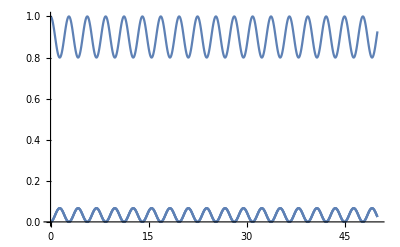

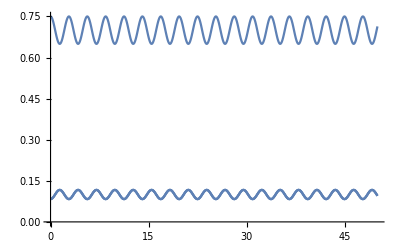

```mathematica
Plot[Diagonal[reduceddensityN]/.ω->1,{t,0,50}]
Plot[Diagonal[reduceddensity]/.ω->1,{t,0,50}]
```

```mathematica
Dimensions[reduceddensityN]
```

{4,4}